## General Settings

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Games\Dropbox\Research\G-constraints\george

```mathematica
dat2MRS=Import["2mrs_1175_done.dat","Data",SkipLines->1];
ndat2MRS=Length[dat2MRS]
tab2MRS0=Table[{dat2MRS[[i,2]],dat2MRS[[i,3]],dat2MRS[[i,25]]},{i,1,ndat2MRS}];
c=3 10^5;   
tab2MRS=Select[tab2MRS0,#[[3]]/c<=0.01&];
listzkm=Flatten[Table[{tab2MRS[[i,3]]},{i,1,Length[tab2MRS]}]];
Length[listzkm]
listzkmall=Flatten[Table[{tab2MRS0[[i,3]]/c},{i,1,Length[tab2MRS0]}]];
Length[listzkmall]
(*Stores equatorial coordinates while converting to decimal degrees*)
dchi[nsig_,M_]:=2 InverseGammaRegularized[M/2,1-Erf[nsig/(√2)]]//N
(*tabcoord=Table[{FromDMS[tab2MRS[[i,1]]]*15,FromDMS[tab2MRS[[i,2]]]},{i,1,Length[tab2MRS]}];*)
tabcoord=Table[{tab2MRS[[i,1]],tab2MRS[[i,2]]},{i,1,Length[tab2MRS]}];
ticksy={{-1.5707963267948966,-90" °"},{-1.27,-75" °"},{-1.07,-60" °"},{-0.835,-45" °"},{-0.57,-30" °"},{-0.28,-15" °"},{0.29,15" °"},{0.57,30" °"},{0.835,45" °"},{1.07,60" °"},{1.285,75" °"}};
ticksx={{-2.82,0" °"},{-2.36,30" °"},{-1.89,60" °"},{-1.42,90" °"},{-0.949,120" °"},{-0.47,150" °"},{0.479,210" °"},{0.94,240" °"},{1.41,270" °"},{1.89,300" °"},{2.35,330" °"},{2.82,360" °"}};
```

43534

3203

43534

```mathematica
tab2MRS
```

{{10.6847,41.2688,-300},{11.8881,-25.2888,243},{148.888,69.0653,-34},{201.366,-43.0187,547},{196.364,-49.4679,563},{23.4621,30.6599,-179},{148.968,69.6797,203},{56.7021,68.0961,31},{204.254,-29.8658,513},{189.998,-11.6231,1024},{10.6743,40.8652,-200},{192.721,41.1202,308},{194.182,21.6827,408},{308.718,60.1537,40},{187.445,8.00041,997},{202.47,47.1953,463},{184.74,47.3037,448},3169,{138.719,79.1962,1957},{208.258,39.5806,2501},{307.651,55.3162,2847},{149.864,-64.731,1728},{22.0934,-65.2709,1645},{192.3,-41.5446,2864},{178.904,1.23731,1885},{197.294,-40.9083,2538},{73.6854,-62.7998,1406},{219.957,-0.71844,1772},{7.21305,28.9396,2169},{137.89,51.2543,2177},{243.87,18.9049,2311},{252.598,55.8386,2115},{179.322,49.2833,785},{245.896,45.7454,1844},{202.207,46.2623,2620}}
 |  |  |  |

## Redshift Analysis

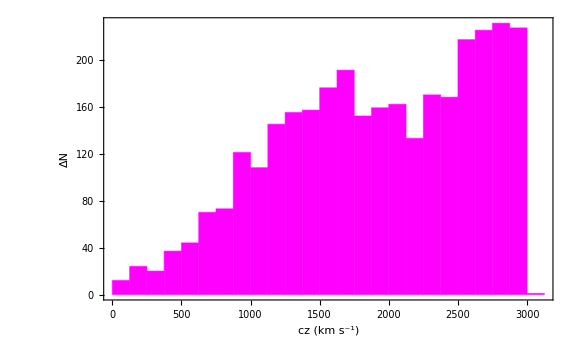

```mathematica
plhist=Histogram[Select[listzkm,#>=0 &],{"Raw",25},ChartStyle->Magenta,Frame->True,FrameLabel->{"cz (km s^-1)","ΔN"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImageSize->Large]
```

```mathematica
Export[NotebookDirectory[]<>"Histogram_2MRS.pdf",plhist,ImageResolution->1000];
```

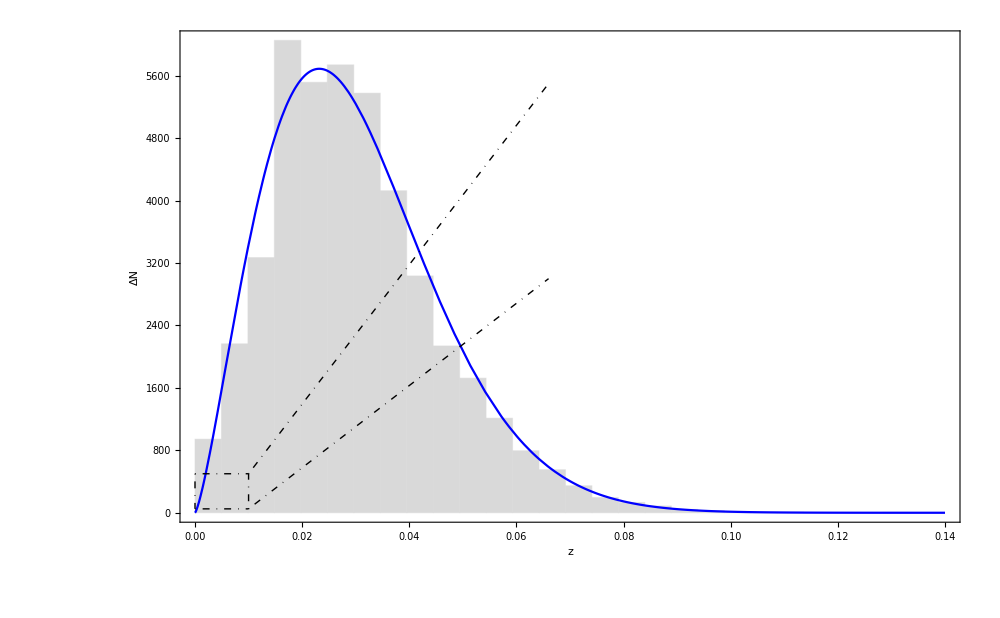

```mathematica
b=1.64;
z0=0.0266;
m=1.31;
Ng=43534;
dNdz[z_]:=Ng*b/(z0*Gamma[(m+1)/b])(z/z0)^m Exp[-(z/z0)^b]
pl1=Histogram[Select[listzkmall,#>=0 &],{"Raw",36},ChartStyle->LightGray,Frame->True,FrameLabel->{"z","ΔN"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImageSize->Large,PlotRange->{{0,0.14},Automatic}];
pl2=Plot[0.005dNdz[z],{z,0,0.14},PlotStyle->Blue,Frame->True,FrameLabel->{"z","N (10^3)"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImageSize->Large];
pl3=Plot[0.0005dNdz[z],{z,0,0.01},PlotStyle->Blue,Frame->True,FrameLabel->{"z","N (10^3)"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImageSize->Large];
pl4=Histogram[Select[listzkm/c,#>=0 &],{"Raw",20},ChartStyle->Magenta,Frame->True,FrameLabel->{"z","ΔN"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImageSize->450];
plin=Show[pl4,pl3];
pldist=Show[pl1,pl2,Epilog->{Inset[plin,Scaled[{0.70,0.65}]],DotDashed,Darker[Black,0.5],Line[{{0,500},{0.01,500}}],Line[{{0.01,500},{0.066,5500}}],Line[{{0,50},{0.01,50}}],Line[{{0,500},{0,50}}],Line[{{0.01,50},{0.01,500}}],Line[{{0.01,50},{0.066,3000}}]},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->1000]
```

```mathematica
Export[NotebookDirectory[]<>"Distribution_2MRS.pdf",pldist,ImageResolution->1000];
```

### χ^2 Minimization Process

```mathematica
listzkmbins=BinLists[Select[listzkm,#>=100 &],120];
ogsublengths=Map[Length,listzkmbins,{1}];
Length[ogsublengths]
```

25

```mathematica
Length[Select[listzkm,#>=100 &]]
```

3168

```mathematica
(*listdNdatog={};
listdNdat={};
sigma=300;
Do[AppendTo[listdNdatog,{Mean[{listzkmbins[[i,1]],listzkmbins[[i,ogsublengths[[i]]]]}],ogsublengths[[i]]}],{i,1,25}]
Do[AppendTo[listdNdat,{Mean[{listzkmbins[[i,1]],listzkmbins[[i,ogsublengths[[i]]]]}]-RandomVariate[NormalDistribution[0,sigma]],ogsublengths[[i]]}],{i,1,25}]
listdNdat=Drop[listdNdat,1];
listdNdatog=Drop[listdNdatog,1];
listdNdat
listdNdatog*)
```

{{607.711,22},{16.6989,20},{415.712,32},{6.40595,43},{909.845,61},{421.903,68},{532.149,108},{1374.53,105},{1024.61,125},{1726.37,138},{1663.46,153},{1597.33,175},{1670.77,166},{1818.46,174},{1439.69,148},{2239.18,151},{2619.85,150},{1573.13,132},{2758.65,159},{2090.56,172},{2555.89,199},{2626.99,219},{2789.16,227},{2609.68,220}}

{{401/2,22},{525/2,20},{410,32},{1027/2,43},{645,61},{1573/2,68},{875,108},{1993/2,105},{2267/2,125},{2581/2,138},{2831/2,153},{3073/2,175},{3309/2,166},{1766,174},{3763/2,148},{3911/2,151},{4217/2,150},{4449/2,132},{2296,159},{2454,172},{2578,199},{5427/2,219},{5719/2,227},{5859/2,220}}

```mathematica
listdNdat={{607.710994884292,22},{16.69885421765514,20},{415.71240240571683,32},{6.405945944162909,43},{909.8452170355399,61},{421.9034215730258,68},{532.1494880422308,108},{1374.5347909873014,105},{1024.606031485068,125},{1726.3734660001355,138},{1663.4590149311043,153},{1597.3302895479696,175},{1670.7715461971795,166},{1818.45899155052,174},{1439.692416359855,148},{2239.179588314595,151},{2619.8541098740548,150},{1573.1309010570176,132},{2758.6468626030946,159},{2090.5584675638356,172},{2555.8949522520147,199},{2626.992746551497,219},{2789.1575681138074,227},{2609.6839061869296,220}};
listdNdatog={{401/2,22},{525/2,20},{410,32},{1027/2,43},{645,61},{1573/2,68},{875,108},{1993/2,105},{2267/2,125},{2581/2,138},{2831/2,153},{3073/2,175},{3309/2,166},{1766,174},{3763/2,148},{3911/2,151},{4217/2,150},{4449/2,132},{2296,159},{2454,172},{2578,199},{5427/2,219},{5719/2,227},{5859/2,220}};
```

```mathematica
test={};
testog={};
Do[AppendTo[testog,listdNdatog⟦i,1⟧-Mean[{listzkmbins⟦i+1,1⟧,listzkmbins⟦i+1,ogsublengths⟦i+1⟧⟧}]],{i,1,24}]
Do[AppendTo[test,listdNdat⟦i,1⟧-Mean[{listzkmbins⟦i+1,1⟧,listzkmbins⟦i+1,ogsublengths⟦i+1⟧⟧}]],{i,1,24}]
test
testog
Length[listdNdat]
Length[listdNdatog]
```

{407.211,-245.801,5.7124,-507.094,264.845,-364.597,-342.851,378.035,-108.894,435.873,247.959,60.8303,16.2715,52.459,-441.808,283.68,511.354,-651.369,462.647,-363.442,-22.105,-86.5073,-70.3424,-319.816}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

24

24

```mathematica
(* Construction of χ^2*)
DN[dN_,dH_,cz_,czt_]:=dN*(cz/listdNdat[[1,1]])^2 (1-dH*HeavisideTheta[cz-czt])^-3;

chi2[dN_,dH_,czt_,s_]:=Sum[(listdNdatog[[i,2]]-DN[dN,dH,listdNdat[[i,1]],czt])^2/(Length[listdNdatog]/listdNdatog[[i,2]]+s^2),{i,1,Length[listdNdat]}];
```

```mathematica
NMinimize[{chi2[dN,dH,czt,0],dN>0, -0.5<dH<0, 1500<czt && czt<2000},{dN,dH,czt}]
```

{157643.,{dN→21.5363,dH→-0.264344,czt→1835.06}}

```mathematica
chmin2bf={157642.92929917312,{dN->21.536306080183763,dH->-0.2643435337109766,czt->1835.0626753910806}};
```

```mathematica
sbf=NSolve[{chi2[chmin2bf[[2,1,2]],chmin2bf[[2,2,2]],chmin2bf[[2,3,2]],s]==Length[Select[listzkm,#>=100 &]]&&s>0},s]
```

{{s→3.09713}}

```mathematica
(*chminfm=FindMinimum[chi2[dN,dH,czt],{{dN,15},{dH},{czt,1500}}];**)
```

```mathematica
chmin2=NMinimize[{chi2[dN,dH,czt,sbf[[1,1,2]]],dN>0, -0.5<dH<0, 1750<czt && czt<3000},{dN,dH,czt}]
```

{3158.94,{dN→21.6423,dH→-0.273673,czt→1954.26}}

```mathematica
chi2[chmin2bf[[2,1,2]],chmin2bf[[2,2,2]],chmin2bf[[2,3,2]],sbf[[1,1,2]]]
```

3168.

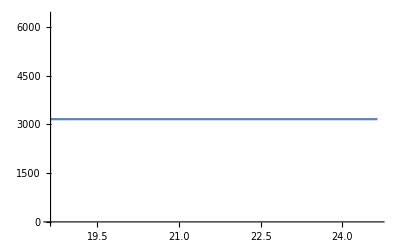

```mathematica
Plot[chi2[chmin2[[2,1,2]],chmin2[[2,2,2]],chmin2[[2,3,2]],sbf[[1,1,2]]],{x,chmin2[[2,1,2]]-3,chmin2[[2,1,2]]+3}]
```

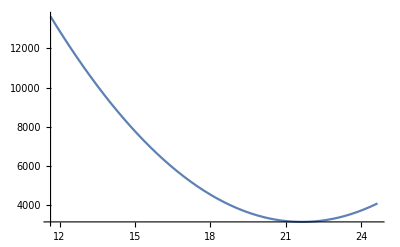

```mathematica
Plot[chi2[x,chmin2[[2,2,2]],chmin2[[2,3,2]],sbf[[1,1,2]]],{x,chmin2[[2,1,2]]-10,chmin2[[2,1,2]]+3}]
```

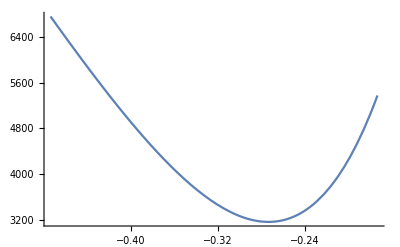

```mathematica
Plot[chi2[chmin2[[2,1,2]],y,chmin2[[2,3,2]],sbf[[1,1,2]]],{y,chmin2[[2,2,2]]-0.2,chmin2[[2,2,2]]+0.1}]
```

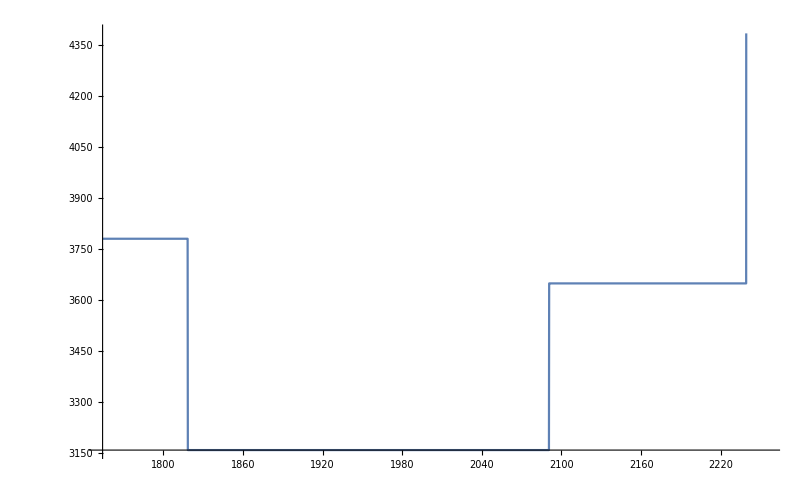

```mathematica
Plot[chi2[chmin2[[2,1,2]],chmin2[[2,2,2]],z,sbf[[1,1,2]]],{z,chmin2[[2,3,2]]-200,chmin2[[2,3,2]]+300}]
```

```mathematica
errdnlist={};
errdnlist=Table[{listdNdatog[[i,1]],Around[listdNdatog[[i,2]],{-(Length[listdNdatog]/listdNdatog[[i,2]]+sbf[[1,1,2]]^2),(Length[listdNdatog]/listdNdatog[[i,2]]+sbf[[1,1,2]]^2)}]},{i,1,Length[listdNdatog]}];
errdnlist2={};
errdnlist2=Table[{listdNdat[[i,1]],Around[listdNdat[[i,2]],{-(Length[listdNdat]/listdNdat[[i,2]]+sbf[[1,1,2]]^2),(Length[listdNdat]/listdNdat[[i,2]]+sbf[[1,1,2]]^2)}]},{i,1,Length[listdNdat]}];
```

```mathematica
pl1=Plot[DN[chmin2[[2,1,2]],chmin2[[2,2,2]],z,chmin2[[2,3,2]]],{z,0,3000},PlotStyle->Blue];
pl2=Histogram[{Select[listzkm,#>=100 &]},25,ChartStyle->Orange,PlotTheme->"Scientific"];
pl3=ListPlot[errdnlist2,PlotStyle->Magenta];
(*pl4=Plot[nlm[cz],{cz,0,3000},PlotStyle->Red];
Show[pl4,pl3]*)
(*pltrans=Show[pl3,pl1,Frame->True,FrameLabel->{"cz (km s^-1)","dN"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImageSize->Large]*)
```

```mathematica
Export[NotebookDirectory[]<>"dN_cz_plot.pdf",pltrans,ImageResolution->1000];
```

```mathematica
chmin2[[2]]
```

{dN→21.6423,dH→-0.273673,czt→1954.26}

```mathematica
dNbf=chmin2[[2,1,2]];
dHbf=chmin2[[2,2,2]];
cztbf=chmin2[[2,3,2]];
sdN=0.1;
dNstep=0.02;
sdH=0.001;
dHstep=0.0001;
chifun=ListInterpolation[ParallelTable[chi2[dN,dH,cztbf,sbf[[1,1,2]]],{dN,dNbf-sdN,dNbf+sdN,dNstep},{dH,dHbf-sdH,dHbf+sdH,dHstep},DistributedContexts->Automatic],{{dNbf-sdN,dNbf+sdN},{dHbf-sdH,dHbf+sdH}}];
(* Params that we want to calculate the errors *)
params={dN,dH};
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
Fij=1/2 Table[D[chifun[dN,dH],params[[p]],params[[d]]]/.chmin2[[2]],{p,1,Length[params]},{d,1,Length[params]}];
cij=Inverse[Fij];
errors=Sqrt[Diagonal[cij]];
Print["The best fit parameters for dN, dH and czt are: dN = ",dNbf," ± ",errors[[1]],", dH = ",dHbf," ± ",errors[[2]]]
```

The best fit parameters for dN, dH and czt are: dN = 21.6423 ± 0.151698, dH = -0.273673 ± 0.00389142

```mathematica
contour=ContourPlot[chi2[dN,dH,cztbf,sbf[[1,1,2]]],{dN,dNbf-1,dNbf+1},{dH,dHbf-0.05,dHbf+0.05},Contours->{chmin2[[1]]+dchi[1,2],chmin2[[1]]+dchi[2,2],chmin2[[1]]+dchi[3,2]},Frame->True,FrameLabel->{"A","ΔH_0/H_0"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Black,Point[{dNbf,dHbf}]}},ContourShading->{Cyan,RGBColor[0.78,1,0.96],LightCyan, White},PlotRange->{{21,22.5},{-0.25,-0.3}},ImageSize->650];
```

```mathematica
Export[NotebookDirectory[]<>"dH_dN_cont.pdf",contour,ImageResolution->1000];
```

```mathematica
pl4=Plot[{DN[chmin2[[2,1,2]],chmin2[[2,2,2]],z,chmin2[[2,3,2]]],DN[chmin2[[2,1,2]]+errors[[1]],chmin2[[2,2,2]]+errors[[2]],z,chmin2[[2,3,2]]],DN[chmin2[[2,1,2]]-errors[[1]],chmin2[[2,2,2]]-errors[[2]],z,chmin2[[2,3,2]]]},{z,0,3000},PlotStyle->{Blue,Cyan,Cyan},Filling->{2->{{3},Cyan}}];
pltrans=Show[{pl4,pl1,pl3},Frame->True,FrameLabel->{"cz (km s^-1)","ΔN"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImageSize->1000];
```

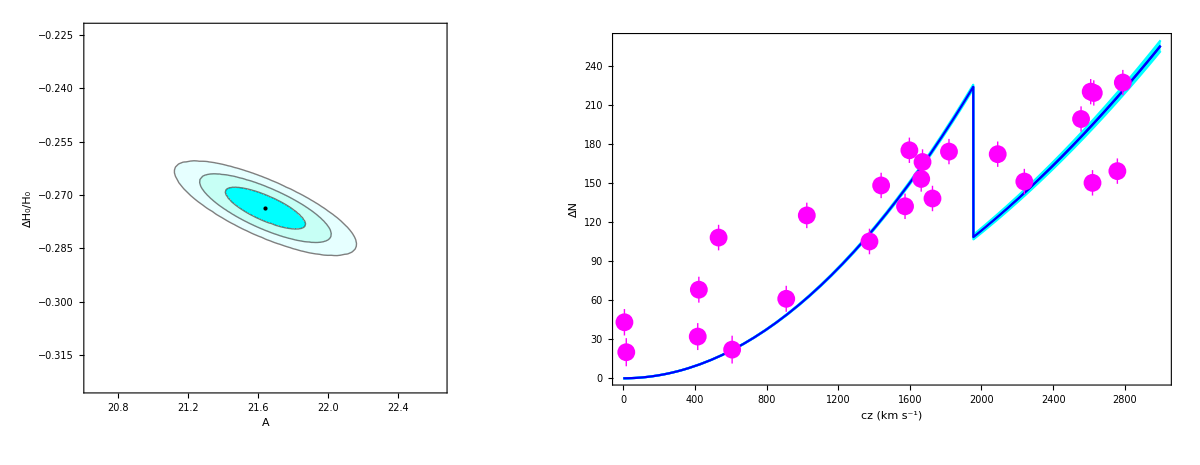

```mathematica
combplt=GraphicsGrid[{{contour,pltrans}},Spacings->-150,ImageSize->1200]
```

```mathematica
Export[NotebookDirectory[]<>"dH_dN__dN_cz_plot_2MRS.pdf",combplt,ImageResolution->1000];
```

## Sky Coverage of 2MRS

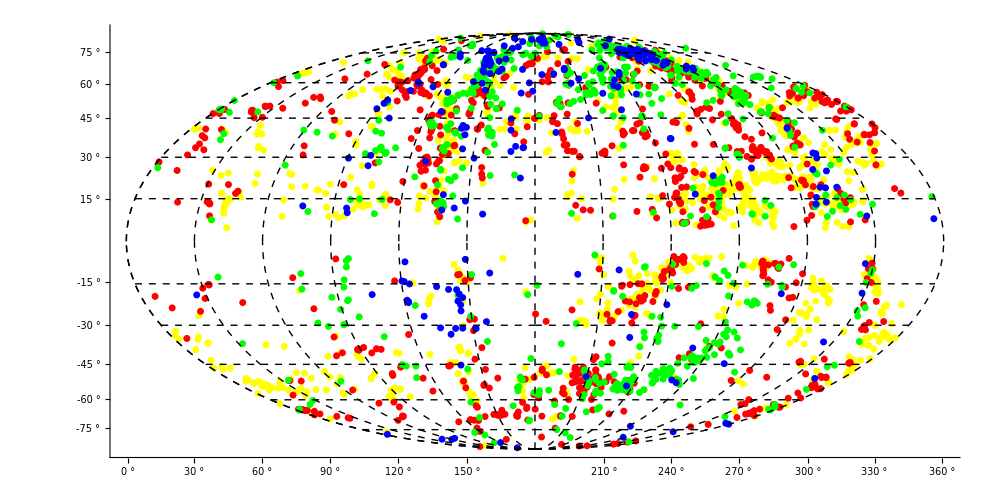

```mathematica
(*Conversion from Equatorial to Galactic coordinates*)
tabcoordgal={};
Do[
sinb=Cos[tabcoord[[i,2]] Degree]Cos[27.4 Degree]Cos[tabcoord[[i,1]] Degree - 192.25 Degree]+Sin[tabcoord[[i,2]] Degree]Sin[27.4 Degree];
b[i]=ArcSin[sinb]/Degree;
y=Sin[tabcoord[[i,2]] Degree]-Sin[b[i] Degree]Sin[27.4 Degree];
x=Cos[tabcoord[[i,2]]Degree] Sin[tabcoord[[i,1]] Degree-192.25 Degree]Cos[27.4 Degree];
l0=ArcTan[y/x]/Degree;
If[y>0 && x>0,l1=l0];
If[y<0 && x>0,l1=l0+360];
If[y>0 && x<0,l1=l0+180];
If[y<0 && x<0,l1=l0+180];
If[y==0 && x>0,l1=0];
If[y==0 && x<0,l1=180];
If[y>0 && x==0,l1=90];
If[y<0 && x==0,l1=270];
l[i]=l1+33;
AppendTo[tabcoordgal,{b[i],l[i]}],{i,1,Length[tabcoord]}]


tab2MRS025=Select[tab2MRS,#[[3]]/c<0.0025&];
tabcoord025=Table[{tab2MRS025[[i,1]],tab2MRS025[[i,2]]},{i,1,Length[tab2MRS025]}];

Clear[l,l0,l1,b]
tabcoordgal025={};
Do[
sinb=Cos[tabcoord025[[i,2]] Degree]Cos[27.4 Degree]Cos[tabcoord025[[i,1]] Degree - 192.25 Degree]+Sin[tabcoord025[[i,2]] Degree]Sin[27.4 Degree];
b[i]=ArcSin[sinb]/Degree;
y=Sin[tabcoord025[[i,2]] Degree]-Sin[b[i] Degree]Sin[27.4 Degree];
x=Cos[tabcoord025[[i,2]]Degree] Sin[tabcoord025[[i,1]] Degree-192.25 Degree]Cos[27.4 Degree];
l0=ArcTan[y/x]/Degree;
If[y>0 && x>0,l1=l0];
If[y<0 && x>0,l1=l0+360];
If[y>0 && x<0,l1=l0+180];
If[y<0 && x<0,l1=l0+180];
If[y==0 && x>0,l1=0];
If[y==0 && x<0,l1=180];
If[y>0 && x==0,l1=90];
If[y<0 && x==0,l1=270];
l[i]=l1+33;
AppendTo[tabcoordgal025,{b[i],l[i]}],{i,1,Length[tabcoord025]}];

(*z<0.0025 sample distribution*)
GeoGraphics[{Orange,AbsolutePointSize@5,Point[GeoPosition@tabcoordgal025]},GeoRange->{{-90,90},{0,360}},GeoGridLinesStyle->Directive[Black,Dashed],GeoProjection->"Mollweide",GeoGridLines->{{-90,90,-75,75,-60,60,-45,45,-30,30,-15,15},{0,30,60,90,120,150,180,210,240,270,300,330,360}},ImageSize->1000,Ticks->{ticksx,ticksy},GeoBackground->White,Axes->True,Background->White,AxesStyle->Black,TicksStyle->Directive[Black,FontSize->19]];

tab2MRS05=Select[tab2MRS,#[[3]]/c>=0.0025 && #[[3]]/c<0.005 &];
tabcoord05=Table[{tab2MRS05[[i,1]],tab2MRS05[[i,2]]},{i,1,Length[tab2MRS05]}];

Clear[l,l0,l1,b]
tabcoordgal05={};
Do[
sinb=Cos[tabcoord05[[i,2]] Degree]Cos[27.4 Degree]Cos[tabcoord05[[i,1]] Degree - 192.25 Degree]+Sin[tabcoord05[[i,2]] Degree]Sin[27.4 Degree];
b[i]=ArcSin[sinb]/Degree;
y=Sin[tabcoord05[[i,2]] Degree]-Sin[b[i] Degree]Sin[27.4 Degree];
x=Cos[tabcoord05[[i,2]]Degree] Sin[tabcoord05[[i,1]] Degree-192.25 Degree]Cos[27.4 Degree];
l0=ArcTan[y/x]/Degree;
If[y>0 && x>0,l1=l0];
If[y<0 && x>0,l1=l0+360];
If[y>0 && x<0,l1=l0+180];
If[y<0 && x<0,l1=l0+180];
If[y==0 && x>0,l1=0];
If[y==0 && x<0,l1=180];
If[y>0 && x==0,l1=90];
If[y<0 && x==0,l1=270];
l[i]=l1+33;
AppendTo[tabcoordgal05,{b[i],l[i]}],{i,1,Length[tabcoord05]}];

(*0.0025<=z<0.005 sample distribution*)
GeoGraphics[{Orange,AbsolutePointSize@5,Point[GeoPosition@tabcoordgal05]},GeoRange->{{-90,90},{0,360}},GeoGridLinesStyle->Directive[Black,Dashed],GeoProjection->"Mollweide",GeoGridLines->{{-90,90,-75,75,-60,60,-45,45,-30,30,-15,15},{0,30,60,90,120,150,180,210,240,270,300,330,360}},ImageSize->1000,Ticks->{ticksx,ticksy},GeoBackground->White,Axes->True,Background->White,AxesStyle->Black,TicksStyle->Directive[Black,FontSize->19]];

tab2MRS075=Select[tab2MRS,#[[3]]/c>=0.005 && #[[3]]/c<0.0075&];
tabcoord075=Table[{tab2MRS075[[i,1]],tab2MRS075[[i,2]]},{i,1,Length[tab2MRS075]}];

Clear[l,l0,l1,b]
tabcoordgal075={};
Do[
sinb=Cos[tabcoord075[[i,2]] Degree]Cos[27.4 Degree]Cos[tabcoord075[[i,1]] Degree - 192.25 Degree]+Sin[tabcoord075[[i,2]] Degree]Sin[27.4 Degree];
b[i]=ArcSin[sinb]/Degree;
y=Sin[tabcoord075[[i,2]] Degree]-Sin[b[i] Degree]Sin[27.4 Degree];
x=Cos[tabcoord075[[i,2]]Degree] Sin[tabcoord075[[i,1]] Degree-192.25 Degree]Cos[27.4 Degree];
l0=ArcTan[y/x]/Degree;
If[y>0 && x>0,l1=l0];
If[y<0 && x>0,l1=l0+360];
If[y>0 && x<0,l1=l0+180];
If[y<0 && x<0,l1=l0+180];
If[y==0 && x>0,l1=0];
If[y==0 && x<0,l1=180];
If[y>0 && x==0,l1=90];
If[y<0 && x==0,l1=270];
l[i]=l1+33;
AppendTo[tabcoordgal075,{b[i],l[i]}],{i,1,Length[tabcoord075]}];

(*0.005<=z<0.0075 sample distribution*)
GeoGraphics[{Orange,AbsolutePointSize@5,Point[GeoPosition@tabcoordgal075]},GeoRange->{{-90,90},{0,360}},GeoGridLinesStyle->Directive[Black,Dashed],GeoProjection->"Mollweide",GeoGridLines->{{-90,90,-75,75,-60,60,-45,45,-30,30,-15,15},{0,30,60,90,120,150,180,210,240,270,300,330,360}},ImageSize->1000,Ticks->{ticksx,ticksy},GeoBackground->White,Axes->True,Background->White,AxesStyle->Black,TicksStyle->Directive[Black,FontSize->19]];

tab2MRS1=Select[tab2MRS,#[[3]]/c>=0.0075 && #[[3]]/c<=0.01&];
tabcoord1=Table[{tab2MRS1[[i,1]],tab2MRS1[[i,2]]},{i,1,Length[tab2MRS1]}];

Clear[l,l0,l1,b]
tabcoordgal1={};
Do[
sinb=Cos[tabcoord1[[i,2]] Degree]Cos[27.4 Degree]Cos[tabcoord1[[i,1]] Degree - 192.25 Degree]+Sin[tabcoord1[[i,2]] Degree]Sin[27.4 Degree];
b[i]=ArcSin[sinb]/Degree;
y=Sin[tabcoord1[[i,2]] Degree]-Sin[b[i] Degree]Sin[27.4 Degree];
x=Cos[tabcoord1[[i,2]]Degree] Sin[tabcoord1[[i,1]] Degree-192.25 Degree]Cos[27.4 Degree];
l0=ArcTan[y/x]/Degree;
If[y>0 && x>0,l1=l0];
If[y<0 && x>0,l1=l0+360];
If[y>0 && x<0,l1=l0+180];
If[y<0 && x<0,l1=l0+180];
If[y==0 && x>0,l1=0];
If[y==0 && x<0,l1=180];
If[y>0 && x==0,l1=90];
If[y<0 && x==0,l1=270];
l[i]=l1+33;
AppendTo[tabcoordgal1,{b[i],l[i]}],{i,1,Length[tabcoord1]}];

(*0.0075<=z<=0.01 sample distribution*)
GeoGraphics[{Orange,AbsolutePointSize@5,Point[GeoPosition@tabcoordgal1]},GeoRange->{{-90,90},{0,360}},GeoGridLinesStyle->Directive[Black,Dashed],GeoProjection->"Mollweide",GeoGridLines->{{-90,90,-75,75,-60,60,-45,45,-30,30,-15,15},{0,30,60,90,120,150,180,210,240,270,300,330,360}},ImageSize->1000,Ticks->{ticksx,ticksy},GeoBackground->White,Axes->True,Background->White,AxesStyle->Black,TicksStyle->Directive[Black,FontSize->19]];
(*Distribution of Binned low-z samples*)
plcoord=GeoGraphics[{Yellow,AbsolutePointSize@5,Point[GeoPosition@tabcoordgal1],Red,AbsolutePointSize@5,Point[GeoPosition@tabcoordgal075],Green,AbsolutePointSize@5,Point[GeoPosition@tabcoordgal05],Blue,AbsolutePointSize@5,Point[GeoPosition@tabcoordgal025]},GeoRange->{{-90,90},{0,360}},GeoGridLinesStyle->Directive[Black,Dashed],GeoProjection->"Mollweide",GeoGridLines->{{-90,90,-75,75,-60,60,-45,45,-30,30,-15,15},{0,30,60,90,120,150,180,210,240,270,300,330,360}},ImageSize->1000,Ticks->{ticksx,ticksy},GeoBackground->White,Axes->True,Background->White,AxesStyle->Black,TicksStyle->Directive[Black,FontSize->19],Epilog->Inset[Framed[Column[{PointLegend[{{Directive[Dashing[{1,1/2,1,1/2,1,1/2}],Blue]},Thick},{"z < 0.0025"},LegendMargins->0],PointLegend[{Directive[Dashing[{1,1/2,1,1/2,1,1/2}],Green],Thick},{"0.0025 ≤ z < 0.005"},LegendMargins->0],PointLegend[{Directive[Dashing[{1,1/2,1,1/2,1,1/2}],Red],Thick},{"0.005 ≤ z < 0.0075"},LegendMargins->0],
PointLegend[{Directive[DotDashed,Yellow],Thick},{"0.0075 ≤ z ≤ 0.01"},LegendMargins->0]}],RoundingRadius->10],Scaled[{0.064,0.92}],BaseStyle -> {FontFamily->"Times",10}]]
```

```mathematica
Export[NotebookDirectory[]<>"galcoord.pdf",plcoord,ImageResolution->1000];
```

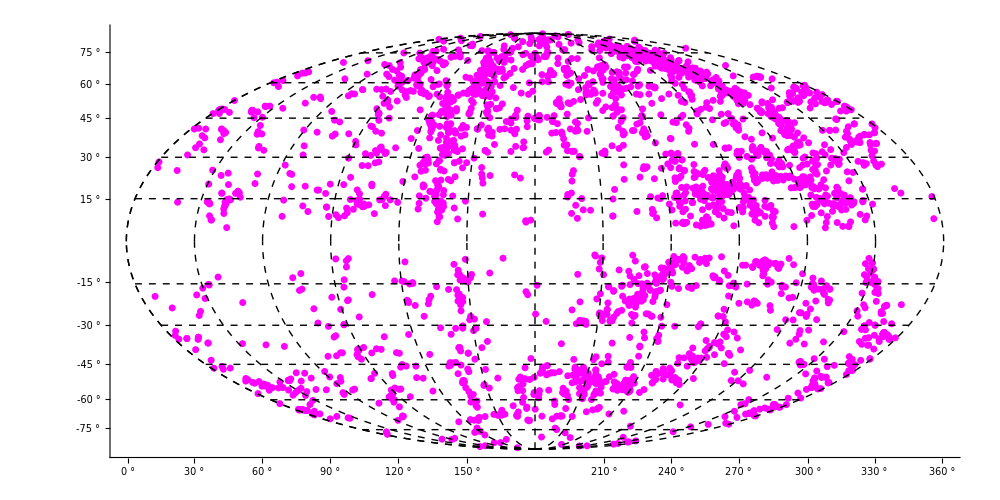

```mathematica
(*Full unbinned low-z sample distribution*)
test=GeoGraphics[{Magenta,AbsolutePointSize@5,Point[GeoPosition@tabcoordgal]},GeoRange->{{-90,90},{0,360}},GeoGridLinesStyle->Directive[Black,Dashed],GeoProjection->"Mollweide",GeoGridLines->{{-90,90,-75,75,-60,60,-45,45,-30,30,-15,15},{0,30,60,90,120,150,180,210,240,270,300,330,360}},ImageSize->1000,Ticks->{ticksx,ticksy},GeoBackground->White,Axes->True,Background->White,AxesStyle->Black,TicksStyle->Directive[Black,FontSize->19]]
```

```mathematica
Export[NotebookDirectory[]<>"skycov2MRS.pdf",test,ImageResolution->1000];
```